z-7 pop1 fit

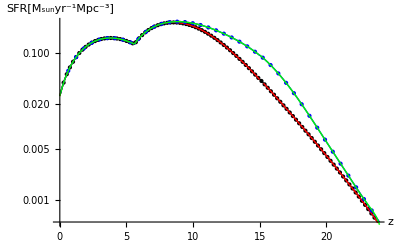

z-17 pop1 fit

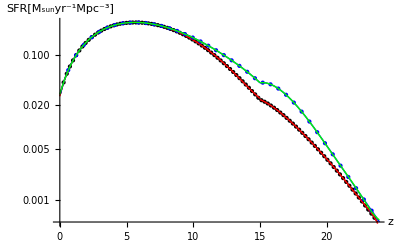

```mathematica
"z-7 pop1 fit"
Show[ListLogPlot[z7pop1w,Joined->True,Mesh->100,PlotStyle-> Black],LogPlot[z7pop1wf[x],{x,0,30},PlotStyle->Red],ListLogPlot[z7pop1s,Joined->True,Mesh->40,PlotStyle-> Blue],LogPlot[z7pop1sf[x],{x,0,30},PlotStyle->{Green}],AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}]
"z-17 pop1 fit"
Show[ListLogPlot[z17pop1w,Joined->True,Mesh->100,PlotStyle-> Black],LogPlot[z17pop1wf[x],{x,0,30},PlotStyle->{Red}],ListLogPlot[z17pop1s,Joined->True,Mesh->40,PlotStyle-> Blue],LogPlot[z17pop1sf[x],{x,0,30},PlotStyle->{Green}],AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}]
```

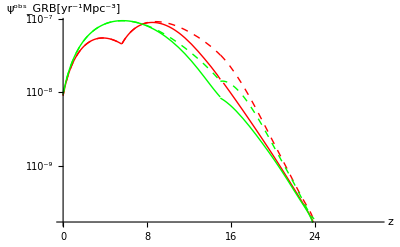

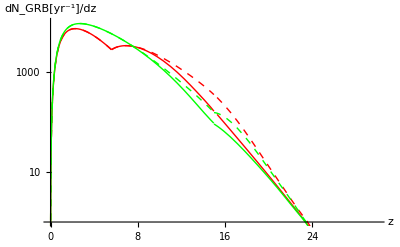

```mathematica
Show[LogPlot[GRBp1[z]*z7pop1wf[z],{z,0,30},PlotStyle->{Red}],LogPlot[GRBp1[z]*z7pop1sf[z],{z,0,30},PlotStyle->{Red,Dashed}],LogPlot[GRBp1[z]*z17pop1wf[z],{z,0,30},PlotStyle->{Green}],LogPlot[GRBp1[z]*z17pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],AxesLabel->{z,"(ψ^obs)_GRB[yr^-1Mpc^-3]"}]
Show[LogPlot[fp1[z]*z7pop1wf[z],{z,0,30},PlotStyle->{Red}],LogPlot[fp1[z]*z7pop1sf[z],{z,0,30},PlotStyle->{Red,Dashed}],LogPlot[fp1[z]*z17pop1wf[z],{z,0,30},PlotStyle->{Green}],LogPlot[fp1[z]*z17pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],AxesLabel->{z,"dN_GRB[yr^-1]/dz"},AxesOrigin->{0,Log[1]},PlotRange->{{0,30},{Log[1],Log[10000]}}]
```

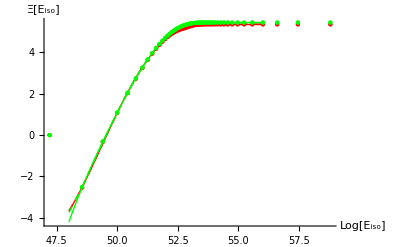

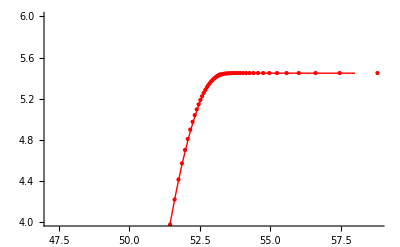

```mathematica
Show[ListPlot[Ξ7w1,Joined->False,PlotStyle->Red],Plot[Ξ7w1fitc[x],{x,48,56},PlotStyle->Red],ListPlot[Ξ7s1,Joined->False,PlotStyle->Red],Plot[Ξ7s1fit[x],{x,48,56},PlotStyle->{Red,Dashed}],ListPlot[Ξ17w1,Joined->False,PlotStyle->Green],Plot[Ξ17w1fit[x],{x,48,56},PlotStyle->Green],ListPlot[Ξ17s1,Joined->False,PlotStyle->Green],Plot[Ξ17s1fitc[x],{x,48,56},PlotStyle->{Green,Dashed}],AxesLabel->{"Log[E_iso]","Ξ[E_iso]"}]
Show[ListPlot[Ξ17s1,Joined->False,PlotStyle->Red,PlotRange->Full],Plot[Ξ17s1fitc[x],{x,48,58},PlotStyle->Red],PlotRange->{4,6}]
```

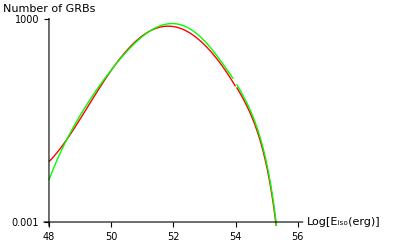

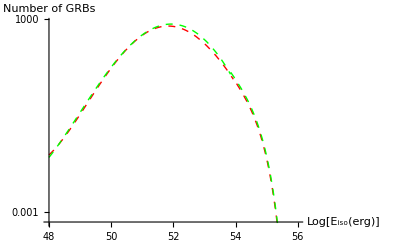

```mathematica
Show[LogPlot[Averageϕiso7w1[x],{x,48,56},PlotStyle->Red,PlotRange->Full],
LogPlot[Averageϕiso17w1[x],{x,48,56},PlotStyle->Green,PlotRange->Full],AxesLabel->{"Log[E_iso(erg)]","Number of GRBs"},PlotRange->{Log[0.001],Log[800]},AxesOrigin->{48,Log[0.001]}]
Show[LogPlot[Averageϕiso7s1[x],{x,48,56},PlotStyle->{Dashed,Red},PlotRange->Full],LogPlot[Averageϕiso17s1[x],{x,48,56},PlotStyle->{Dashed,Green},PlotRange->Full],AxesLabel->{"Log[E_iso(erg)]","Number of GRBs"},PlotRange->{Log[0.0005],Log[800]},AxesOrigin->{48,Log[0.0005]}]
```